```mathematica
SetDirectory["~/Desktop/ipcp/ex12"]
```

/home/zop/Desktop/ipcp/ex12

```mathematica
FileNames["*","/home/zop/Desktop/ipcp/ex12"]
```

{/home/zop/Desktop/ipcp/ex12/81,/home/zop/Desktop/ipcp/ex12/83,/home/zop/Desktop/ipcp/ex12/85,/home/zop/Desktop/ipcp/ex12/a.out,/home/zop/Desktop/ipcp/ex12/Exercises12_ger.pdf,/home/zop/Desktop/ipcp/ex12/rand.c}

```mathematica
data1 = SemanticImport["/home/zop/Desktop/ipcp/ex12/81"];
```

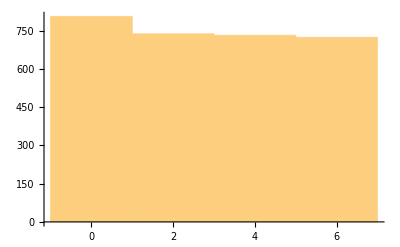

```mathematica
Histogram[data1]
```

```mathematica
data2 = SemanticImport["/home/zop/Desktop/ipcp/ex12/83"];
```

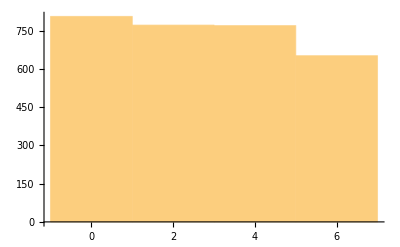

```mathematica
Histogram[data2]
```

```mathematica
data3 = SemanticImport["/home/zop/Desktop/ipcp/ex12/85"];
```

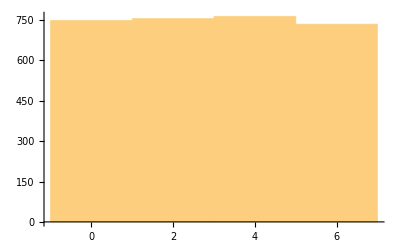

```mathematica
Histogram[data3]
```

```mathematica
snakes = SemanticImport["/home/zop/Desktop/ipcp/ex12/histo_snakes_myrandom"];
```

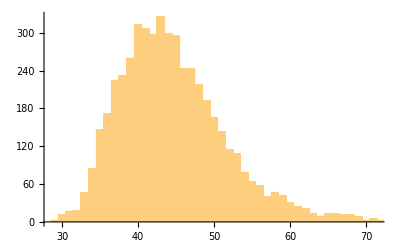

```mathematica
Histogram[snakes, 60]
```

```mathematica
Median[snakes]
```

44

```mathematica
Max[snakes]
```

85

```mathematica
Min[snakes]
```

29

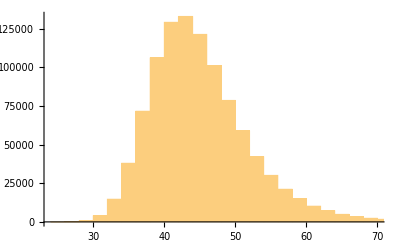

```mathematica
snakesc = SemanticImport["/home/zop/Desktop/ipcp/ex12/histo_snakes_crandom"];
Histogram[snakesc,60]
```